## General : One cooperative energy (loop penalty)

```mathematica
gF=.; gbF=.; gb=.; gp=.;  β =.; m=.; n=.
```

Note : β = 1/RT  in units of mol/kcal  gives β = 1.68
             Tamayo et al, Cell Reports 19, 150 (2017) suggests exp(-β gb) = 0.2 x10^-6, i.e.  β g_b=15.4
ρ  is given in mol/liter.

gF: Folding energy
gbF: Binding energy to a folded quadruplex 
gb: Binding energy, regular
gp: Penalty for a loop (cooperative energy)
m: Number of binding sites per quadruplex (m=4)
n: Number of binding domains on the protein (n=3)

Reference: Unfolded RNA without bound protein
state: Vector {l1,l2,..lj} characterizing number of bonds for j bounded proteins

```mathematica
loops[state_] := Sum[state[[i]]-1, {i,1,Length[state]}];
combifactor[state_,i_]:= Binomial[n-1,state[[i]]-1]/state[[i]];
```

## General case

```mathematica
cc[state_] :=(n*Exp[βgb]ρ)^j *m!/(j!*(m-j-l)!)*Product[combifactor[state,i]*Exp[(state[[i]]-1)(βgb-βgp)],{i,1,Length[state]}] //. {j -> Length[state], l -> loops[state]} ;
```

```mathematica
values = {m -> 4, n -> 3}; 

cF = Exp[βgF]; 
c1F = cF*cc[{1}] //. βgb -> βgbF //. values;
c1 = cc[{1}] //.  values;
c2 =cc[{2}] //. values;
c3 =cc[{3}]//. values;
c11 =cc[{1,1}] //. values;
c12 =cc[{1,2}] //. values;
c13 =cc[{1,3}] //. values;
c22 =cc[{2,2}] //. values;
c111=cc[{1,1,1}] //. values;
c112 =cc[{1,1,2}] //. values;
c1111=cc[{1,1,1,1}] //. values;

cbound =c1+c2+c3+c11+c12+c13+c22+c111+c112+c1111;
ctotal = cF+1+cbound;
hill[ρ_,βgF_,βgb_,βgp_] =cbound/ctotal;
```

144 ⅇ^(4 βgb-2 βgp) ρ^2

(144 ⅇ^(4 βgb-2 βgp) ρ^2)/(1+ⅇ^βgF+144 ⅇ^(4 βgb-2 βgp) ρ^2)

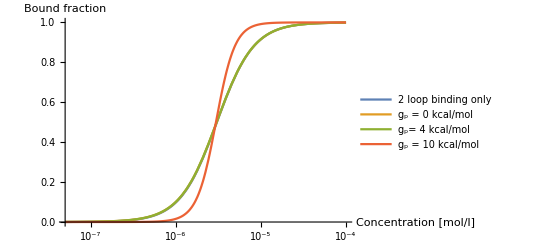

```mathematica
cboundreduced =  c13+c22 //FullSimplify
hillreduced[ρ_,βgF_,βgb_,βgp_]=  cboundreduced/(1+cF+cboundreduced)
β=1.68;
LogLinearPlot[{hillreduced[ρ, β*24.5,15.4,0],hill[ρ,β*24.5,15.4,0],hill[ρ,β*16.5,15.4,β*4], hill[ρ,β*9.04,15.4, β*10]},{ρ,5*10^(-8),10^(-4)},AxesLabel -> {"Concentration [mol/l]", "Bound fraction"}, PlotLegends -> { "2 loop binding only", "g_p = 0 kcal/mol", "g_p= 4 kcal/mol","g_p = 10 kcal/mol"}]
```

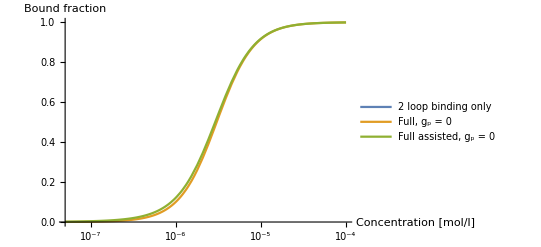

```mathematica
cboundassisted = c1F +  c1+c2+c3+c11+c12+c13+c22+c111+c112+c1111;
hillassisted[ρ_,βgF_,βgb_,βgp_,βgbF_] = (cboundassisted)/(1+cF + cboundassisted);
β=1.68;
LogLinearPlot[{hillreduced[ρ, β*24.5,15.4,0],hill[ρ,β*24.5,15.4,0],hillassisted[ρ,β*24.5,15.4,0,15.4/2] },{ρ,5*10^(-8),10^(-4)},AxesLabel -> {"Concentration [mol/l]", "Bound fraction"}, PlotLegends -> { "2 loop binding only", "Full, g_p = 0", "Full assisted, g_p = 0"}]
```

```mathematica
kk[βgF_,βgb_,βgp_] := ρ //. FindRoot[hill[ρ,βgF,βgb,βgp]   ==0.5,{ρ,0.000003}];
kkassisted[βgF_,βgb_,βgp_, βgbF_] := ρ //. FindRoot[hillassisted[ρ,βgF,βgb,βgp, βgbF]   ==0.5,{ρ,0.000003}];
x9[βgF_,βgb_,βgp_] := ρ //. FindRoot[hill[ρ,βgF ,βgb,βgp]==0.9,{ρ,0.00001}];
x1[βgF_,βgb_,βgp_] := ρ //. FindRoot[hill[ρ,βgF ,βgb,βgp]==0.1,{ρ,0.000000001}];
hillcoeff1[βgF_,βgb_,βgp_]:= Log[81.]/Log[x9[βgF,βgb,βgp]/x1[βgF,βgb,βgp]]
hillcoeff2[βgF_,βgb_,βgp_] := 4 ρ D[hill[ρ,βgF,βgb,βgp],ρ] //. ρ -> kk[βgF,βgb,βgp]
nhassisted[βgF_,βgb_,βgp_,βgbF_] := 4 ρ D[hillassisted[ρ,βgF,βgb,βgp,βgbF],ρ] //. ρ -> kkassisted[βgF,βgb,βgp,βgbF]
```

```mathematica
ktarget=3*10^(-6); β=1.68;
ggF[βgb_,βgp_]:= βgF //. FindRoot[hill[ktarget,βgF,βgb,βgp]   ==0.5,{βgF,betagF[0,βgb, βgp]}];
ggFassisted[βgb_,βgp_, βgbF_]:= βgF //. FindRoot[hillassisted[ktarget,βgF,βgb,βgp, βgbF]   ==0.5,{βgF,ggF[βgb, βgp]}];
```

## Special cases: Zero or infinite loop penalty

```mathematica
zf=.; zb=.;  β = .;
```

```mathematica
cc0[state_] :=(n*zb*ρ)^j *m!/(j!*(m-j-l)!)*Product[combifactor[state,i]zb^((state[[i]]-1)),{i,1,Length[state]}] //. {j -> Length[state], l -> loops[state]}
```

### No loop penalty

```mathematica
values = {m -> 4, n -> 3}; 

c0F = zf;
c01 = cc0[{1}] //.  values;
c02=cc0[{2}] //. values;
c03 =cc0[{3}]//. values;
c011 =cc0[{1,1}] //. values;
c012 =cc0[{1,2}] //. values;
c013 =cc0[{1,3}] //. values;
c022 =cc0[{2,2}] //. values;
c0111=cc0[{1,1,1}] //. values;
c0112 =cc0[{1,1,2}] //. values;
c01111=cc0[{1,1,1,1}] //. values;

c0bound = c01+c011+c0111+c01111+c02+c012+c0112+c03+c013+c022;
c0total =1+c0F+c0bound;
hill0[ρ_,zf_,zb_] =c0bound/c0total
```

(12 zb ρ+36 zb^2 ρ+24 zb^3 ρ+54 zb^2 ρ^2+108 zb^3 ρ^2+144 zb^4 ρ^2+108 zb^3 ρ^3+108 zb^4 ρ^3+81 zb^4 ρ^4)/(1+zf+12 zb ρ+36 zb^2 ρ+24 zb^3 ρ+54 zb^2 ρ^2+108 zb^3 ρ^2+144 zb^4 ρ^2+108 zb^3 ρ^3+108 zb^4 ρ^3+81 zb^4 ρ^4)

```mathematica
kk0[zf_,zb_ ] = x //. Solve[hill0[x,zf,zb] ==1/2,x][[4]];
nh0[zf_,zb_] := 4 x D[hill0[x,zf,zb],x] //. x -> kk0[zf,zb] ;
```

### No loops (i.e., infinite loop penalty)

```mathematica
values = {m -> 4, n -> 3}; 

c0F = zf;
c01 = cc0[{1}] //.  values;
c011 =cc0[{1,1}] //. values;
c0111=cc0[{1,1,1}] //. values;
c01111=cc0[{1,1,1,1}] //. values;

cinfbound = c01+c011+c0111+c01111;
cinftotal =1+c0F+cinfbound;
hillinf[ρ_,zf_,zb_] =cinfbound/cinftotal
```

(12 zb ρ+54 zb^2 ρ^2+108 zb^3 ρ^3+81 zb^4 ρ^4)/(1+zf+12 zb ρ+54 zb^2 ρ^2+108 zb^3 ρ^3+81 zb^4 ρ^4)

```mathematica
kkinf[zf_,zb_ ] = FullSimplify[x //. Solve[hillinf[x,zf,zb] ==1/2,x][[4]], Assumptions -> {zf>0,zb>0}]
nhinf[zf_] = FullSimplify[4 x D[hillinf[x,zf,zb],x] //. x -> kkinf[zf,zb], Assumptions -> {zf>0,zb>0}]
```

(-1+(2+zf)^(1/4))/(3 zb)

(4 (2+zf-(2+zf)^(3/4)))/(1+zf)

## Graphics for paper

```mathematica
Shapes of Hill curves at  Subscript[g, b]=9.2 kcal/mol, i.e.  Subscript[βg, b]=15.4  
setting Subscript[g, F] such that  K = 3*10^-6 mol/l
```

```mathematica
β=1.68;
```

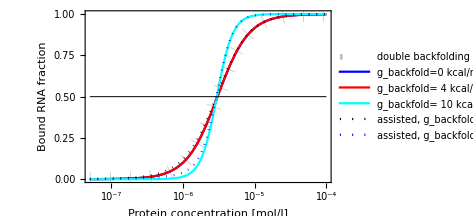

```mathematica
graph0=LogLinearPlot[{hillreduced[ρ, β*24.5,15.4,0],hill[ρ,β*24.5,15.4,0],hill[ρ,β*16.5,15.4,β*4],hill[ρ,β*9.04,15.4, β*10],  hillassisted[ρ,β*24.5,15.4, 0,15.4/2],hillassisted[ρ,β*9.04,15.4, β*10,15.4/2],0.5},{ρ,5*10^(-8),10^(-4)},    Frame -> {True, True, False, False}, FrameLabel-> {"Protein concentration [mol/l]", "Bound RNA fraction"}, LabelStyle -> {Black,16},RotateLabel -> True,  PlotLegends -> { "double backfolding model", "g_backfold=0 kcal/mol", "g_backfold= 4 kcal/mol","g_backfold= 10 kcal/mol",  "assisted, g_backfold= 0 kcal/mol","assisted, g_backfold= 10 kcal/mol" }, PlotStyle -> { {Lighter[Gray,.5],Thickness[0.03],Dashing[{0.,0.04} ]},{Blue,Thick}  ,{Red,Thick},{Cyan, Thick}, {Black,Dashing[{0,Small}]},  {Blue,Dashing[{0,Small}]},{Black, Thickness[0.002]}} , ImageSize -> 350]
```

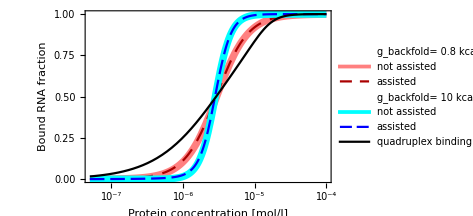

```mathematica
graph1=LogLinearPlot[{, hill[ρ,β*23,β*9.2,β*0.8],  hillassisted[ρ,β*23,β*9.2, β*0.8,β*4],,hill[ρ,β*23,β*12.7, β*10],
hillassisted[ρ,β*23,β*12.7, β* 10,β*4],
hillassisted[ρ,β*23,β*12, β* 8.,β*6.1]},{ρ,5*10^(-8),10^(-4)},    Frame -> {True, True, False, False}, FrameLabel-> {"Protein concentration [mol/l]", "Bound RNA fraction"}, LabelStyle -> {Black,16},RotateLabel -> True,  PlotLegends -> {  "g_backfold= 0.8 kcal/mol","not assisted", "assisted","g_backfold= 10 kcal/mol", "not assisted", "assisted" ,
"quadruplex binding dominant"}, PlotStyle -> {{White}, {Lighter[Red,0.5],Thickness[0.015]},{Darker[Red],Dashing[{0.03,0.02}]},{White},{Cyan, Thickness[0.015]},   {Blue,Dashing[{0.03,0.012} ]},{Black,Thick}} , ImageSize -> 350]
```

```mathematica
Hill coefficients at  Subscript[g, p]=0  versus K  (varied by varying  Subscript[g, F] )
```

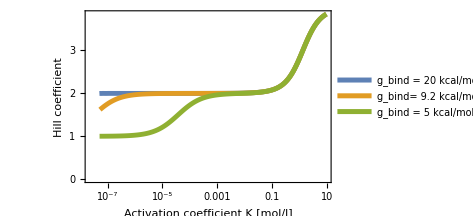

```mathematica
kmin=5*10^(-8);kmax = 10  ;
list[gb_] :=Select[Table [{ kk0[Exp[β gf],Exp[β *gb]], nh0[Exp[β *gf],Exp[β* gb]]},{gf,4*gb-18, 4*gb+13,0.1}],#[[1]]>kmin &&#[[1]] < kmax &];
graph2=ListLogLinearPlot[{list[20],list[9.2],list[5.] }, Joined -> True,AxesLabel -> {"K [mol/l]", "n"},PlotLegends -> {"g_bind = 20 kcal/mol", "g_bind= 9.2 kcal/mol","g_bind = 5 kcal/mol"},     Frame -> {True, True, False, False}, FrameLabel-> {"Activation coefficient K [mol/l]", "Hill coefficient"}, LabelStyle -> {Black,16},RotateLabel -> True,  PlotStyle ->{Thickness[0.01],Thickness[0.01],Thickness[0.01]}, ImageSize-> {350,350}]
```

```mathematica
Hill coefficients at  Subscript[g, p]=Infinity  versus K  (varied by varying  Subscript[g, F] )
```

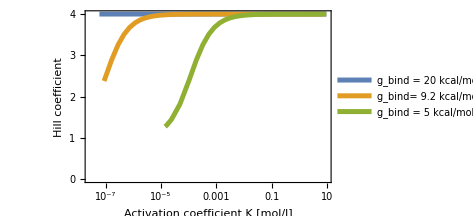

```mathematica
kmin=5*10^(-8);kmax = 10  ;
listinf[gb_] :=Select[Table [{ kkinf[Exp[β gf],Exp[β *gb]], nhinf[Exp[β *gf]]},{gf,-10., 100.,1}],#[[1]]>kmin &&#[[1]] < kmax &];
graph3=ListLogLinearPlot[{listinf[20.],listinf[9.2],listinf[5.] }, Joined -> True,AxesLabel -> {"K [mol/l]", "n"},PlotLegends -> {"g_bind = 20 kcal/mol", "g_bind= 9.2 kcal/mol","g_bind = 5 kcal/mol"},      Frame -> {True, True, False, False}, FrameLabel-> {"Activation coefficient K [mol/l]", "Hill coefficient"}, LabelStyle -> {Black,16},  PlotRange -> All, PlotStyle ->{Thickness[0.01],Thickness[0.01],Thickness[0.01]}, ImageSize -> 350]
```

```mathematica
Folding energies Subscript[g, F]  requiring that  K = 3*10^-6 mol/l
```

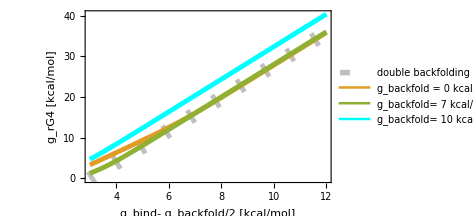

```mathematica
β=1.68; ρc=3.*10^(-6); ktarget = ρc;
betagF[u_,βgb_, βgp_] = Log[144*ρc^2]+4*βgb-2 βgp + u ;
ggF[βgb_,βgp_]:= βgF //. FindRoot[hill[ktarget,βgF,βgb,βgp]   ==0.5,{βgF,betagF[0,βgb, βgp]}];
graph4=Plot[ {betagF[0,β*x,0]/β,ggF[β*x,0]/β ,ggF[β*(x+3.5),β*7]/β,ggF[β*(x+5),β*10]/β },{x,3,12}, AxesLabel -> {"g_b- g_p/2 [kcal/mol]", "g_F [kcal/mol] "} , PlotLegends -> {"double backfolding model", "g_backfold = 0 kcal/mol", "g_backfold= 7 kcal/mol" ,"g_backfold= 10 kcal/mol" },      Frame -> {True, True, False, False}, FrameLabel-> {"g_bind- g_backfold/2 [kcal/mol]", "g_rG4 [kcal/mol]  "},  LabelStyle -> {Black,16}, PlotStyle -> {{Lighter[Gray,.5],Thickness[0.03],Dashing[{0.01,0.05}  ]},  Thickness[0.01]  ,Thickness[0.01], {Cyan, Thickness[0.01]}  },ImageSize->350]
```

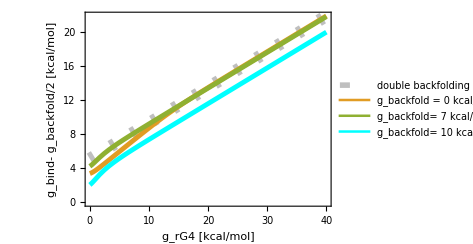

```mathematica
β=1.68; ktarget=3.*10^(-6);  
betagb[k_,βgF_, βgp_] = (βgF- Log[144*k^2]+2 βgp)/4. ;
ggb[βgF_,βgp_]:= βgb //. FindRoot[hill[ktarget,βgF,βgb,βgp]   ==0.5,{βgb,betagb[ktarget,βgF, βgp]}];
graph4= Plot[ { betagb[ktarget, β*gF,0], ggb[ β*gF,0.], ggb[ β*gF,β*7]-3.5*β,ggb[ β*gF,β*10]-5*β}, {gF,0,40},AxesLabel -> {"g_b- g_p/2 [kcal/mol]", "g_F [kcal/mol] "} , PlotLegends -> {"double backfolding model", "g_backfold = 0 kcal/mol", "g_backfold= 7 kcal/mol" ,"g_backfold= 10 kcal/mol" },      Frame -> {True, True, False, False},AspectRatio -> 0.7, FrameLabel-> {"g_rG4 [kcal/mol]","g_bind- g_backfold/2  [kcal/mol]" },  LabelStyle -> {Black,16}, PlotStyle -> {{Lighter[Gray,.5],Thickness[0.025],Dashing[{0.01,0.04}  ]},  Thickness[0.01]  ,Thickness[0.01], {Cyan, Thickness[0.01]}  },ImageSize->350]
```

```mathematica
graph5=Plot[{hillcoeff2[ggF[β*8.8+β*gp/2,β*gp],β*8.8+β*gp/2,β*gp],hillcoeff2[ggF[β*7+β*gp/2,β*gp],β*7+β*gp/2,β*gp],hillcoeff2[ggF[β*6+β*gp/2,β*gp],β*6+β*gp/2,β*gp]}  ,{gp,0,14}, PlotRange -> {0,4.1},Axes -> None, PlotLegends -> {"g_bind= g_backfold/2 + 8.8 kcal/mol","g_bind= g_backfold/2 + 7 kcal/mol",  "g_bind= g_backfold/2 + 6 kcal/mol"}, PlotStyle ->{Thickness[0.01],Thick ,Thickness[0.01]},      Frame -> {True, True, False, False}, FrameLabel-> {"g_backfold[kcal/mol]", "Hill coefficient"}, LabelStyle -> {Black,16},ImageSize->350 ]
```

$Aborted

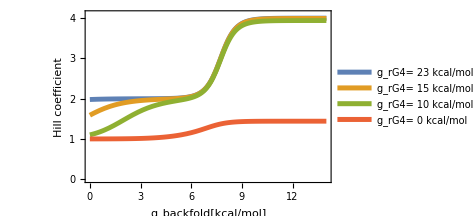

```mathematica
β=1.68; ktarget=3.*10^(-6);  
betagb[k_,βgF_, βgp_] = (βgF- Log[144*k^2]+2 βgp)/4. ;
ggb[βgF_,βgp_]:= βgb //. FindRoot[hill[ktarget,βgF,βgb,βgp]   ==0.5,{βgb,betagb[ktarget,βgF, βgp]}];
hillcoeff3[k_,βgF_,βgb_,βgp_] :=  4 ρ D[hill[ρ,βgF,βgb,βgp],ρ] //. ρ -> k  
graph5=Plot[{hillcoeff3[ktarget,β*23,ggb[β*23,β*gp] ,β*gp],hillcoeff3[ktarget,β*15,ggb[β*15,β*gp] ,β*gp],hillcoeff3[ktarget,β*10,ggb[β*10,β*gp],β*gp],
hillcoeff3[ktarget,β*0,ggb[β*0,β*gp],β*gp]}  ,{gp,0,14}, PlotRange -> {0,4.1},Axes -> None, PlotLegends -> {"g_rG4= 23 kcal/mol","g_rG4= 15 kcal/mol",  "g_rG4= 10 kcal/mol", "g_rG4= 0 kcal/mol"}, PlotStyle ->{Thickness[0.01] },      Frame -> {True, True, False, False}, FrameLabel-> {"g_backfold[kcal/mol]", "Hill coefficient"}, LabelStyle -> {Black,16},ImageSize->350 ]
```

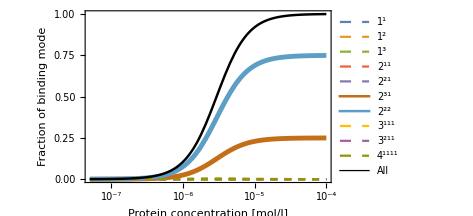

```mathematica
energies = {βgF -> 1.68*23, βgb-> 1.68*9.2, βgp -> 1.68*0.8};
 graph6=LogLinearPlot[{  c1/ctotal//. energies, c2/ctotal//. energies, c3/ctotal//. energies, c11/ctotal//. energies, c12/ctotal//. energies, c13/ctotal//. energies, c22/ctotal//. energies, c111/ctotal//. energies, c112/ctotal//. energies, c1111/ctotal//. energies,cbound/ctotal//. energies},{ρ,5*10^(-8),10^(-4)},PlotRange -> All, AxesLabel -> {"Concentration [mol/l]", "Bound fraction"}, PlotLegends -> { "1^1","1^2","1^3","2^11","2^21","2^31","2^22","3^111","3^211","4^1111", "All"},Frame -> {True, True, False, False},  FrameLabel-> {"Protein concentration [mol/l]", "Fraction of binding mode"} ,RotateLabel -> True, LabelStyle -> {Black,16},  PlotStyle ->{{Thick,Dashed},{Thick,Dashed},{Thick,Dashed},{Thick,Dashed},{Thick,Dashed},{Thickness[0.01]},{Thickness[0.01]},{Thick,Dashed},{Thick,Dashed},{Thick,Dashed},{Thickness[0.005], Black}},ImageSize->350 ]
```

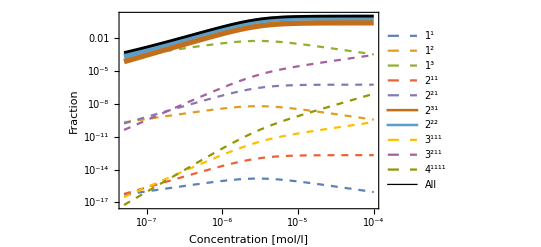

```mathematica
LogLogPlot[{  c1/ctotal//. energies, c2/ctotal//. energies, c3/ctotal//. energies, c11/ctotal//. energies, c12/ctotal//. energies, c13/ctotal//. energies, c22/ctotal//. energies, c111/ctotal//. energies, c112/ctotal//. energies, c1111/ctotal//. energies,cbound/ctotal//. energies},{ρ,5*10^(-8),10^(-4)},PlotRange -> All, AxesLabel -> {"Concentration [mol/l]", "Bound fraction"}, PlotLegends -> { "1^1","1^2","1^3","2^11","2^21","2^31","2^22","3^111","3^211","4^1111", "All"},Frame -> {True, True, False, False}, FrameLabel-> {"Concentration [mol/l]", "Fraction"} ,RotateLabel -> True, LabelStyle -> {Black,16},  PlotStyle ->{{Thick,Dashed},{Thick,Dashed},{Thick,Dashed},{Thick,Dashed},{Thick,Dashed},{Thickness[0.01]},{Thickness[0.01]},{Thick,Dashed},{Thick,Dashed},{Thick,Dashed},{Thickness[0.005], Black}}]
```

```mathematica
Export["hill_quadruplex_raw.svg" ,GraphicsColumn[{graph1,graph2,graph3,graph4,graph5,graph6}, ImageSize -> 1000]]
```

hill_quadruplex_raw.svg